# Short time displacements

## compute displacements

```mathematica
DIM=2;
boxInvTrans[boxmat_,pt_]:=Module[{invmat},
invmat=Inverse[boxmat];
invmat.pt
];
boxTrans[boxmat_,pt_]:=boxmat.pt;
putInBox[boxmat_,pt_]:=Module[{temp},
temp=boxInvTrans[boxmat,pt];
Do[
If[Between[temp[[dd]]==False,{0,1}],temp[[dd]]-=Sign[temp[[dd]]]];
,{dd,1,DIM}];
boxTrans[boxmat,temp]
];
minDist[boxmat_,ptA_,ptB_]:=Module[{vA,vB,disp},
vA=boxInvTrans[boxmat,ptA];
vB=boxInvTrans[boxmat,ptB];
disp=vA-vB;
Do[
If[Abs[disp[[dd]]]>0.5,disp[[dd]]-=Sign[disp[[dd]]]];
,{dd,1,DIM}];
boxTrans[boxmat,disp]
];
```

```mathematica
computeDisplacements[inipts_,pts_,boxmat_]:=Module[{minDists,minLenths,overlaps},
minDists=Table[minDist[boxmat,inipts[[i]],pts[[i]]],{i,1,Length[pts]}]
];
```

## load data

```mathematica
temperatures={"0.06300000","0.00500000","0.00200000"};
```

```mathematica
data=Table[Import["C:\\Users\\cheng\\Downloads\\glassyDynamics_N4096_p3.8250_T"<>temp<>"_waitingTime10000_idx10.nc","Data"],{temp,temperatures}];
```

```mathematica
temperatures
```

{0.06300000,0.00500000,0.00200000}

```mathematica
Normal[data[[1,4,40]]]
```

{10002.8}

```mathematica
temperatures
```

{0.06300000,0.00500000,0.00200000}

```mathematica
Norm[{0.5,0.5}]
```

0.707107

```mathematica
displacements=Table[Table[computeDisplacements[Partition[Normal[data[[temp,3,1]]],2],Partition[Normal[data[[temp,3,time]]],2],Partition[Normal[data[[1,1,1]]],2]],{time,2,Length[data[[1,1]]]}],{temp,3}];
```

```mathematica
magnitudes=Table[Table[Norm/@displacements[[i,time]],{time,Length[data[[1,1]]]-1}],{i,3}];
```

```mathematica
Max[magnitudes[[1,10]]]
```

0.113177

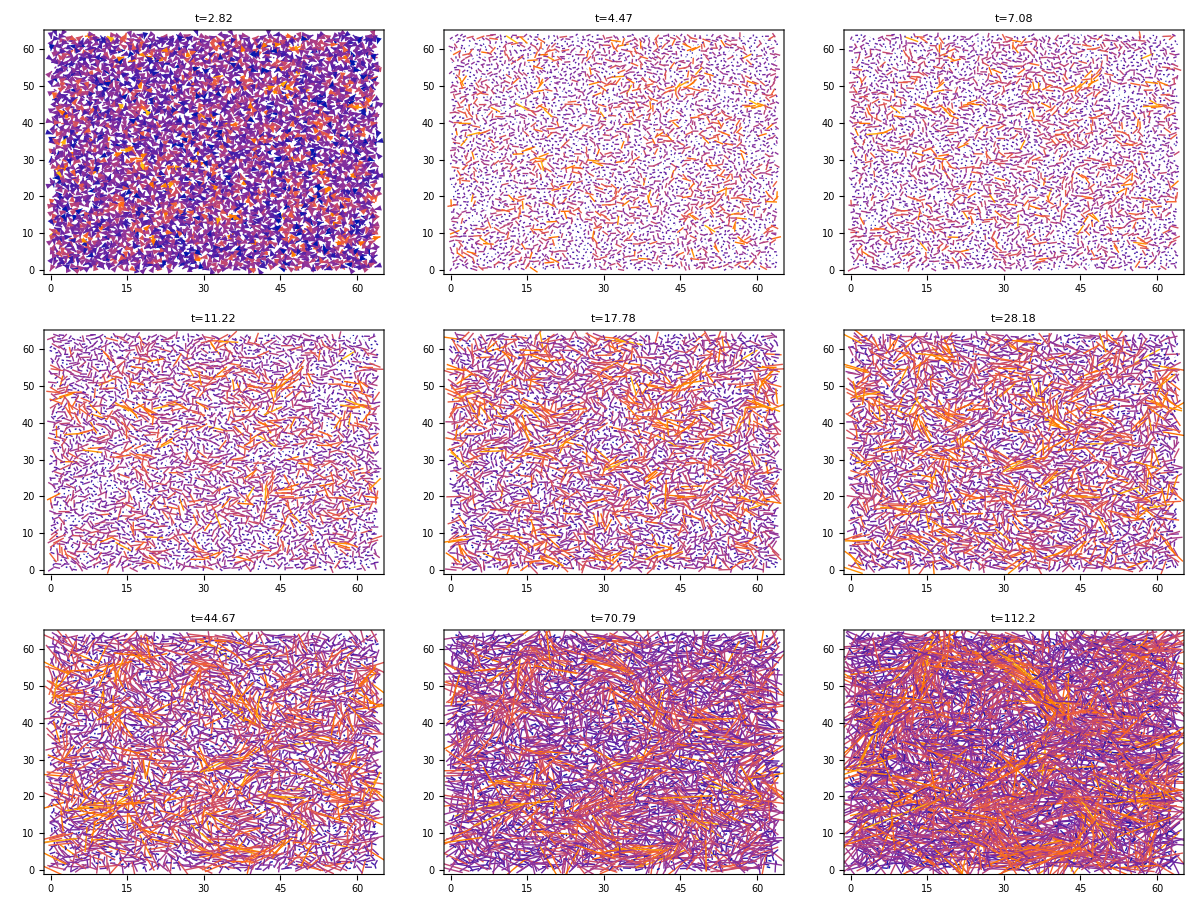

```mathematica
Grid[Partition[Table[ListVectorPlot[Table[{Partition[Normal[data[[1,3,1]]],2][[i]],displacements[[1,time,i]]},{i,4096}],VectorSizes->{0,Max[magnitudes[[1,time]]]},VectorScaling->"Linear",VectorStyle->{Thin,Arrowheads[0.01]},VectorPoints->All,VectorColorFunctionScaling->True,PlotLabel->"t="<>ToString[data[[1,4,time,1]]-data[[1,4,1,1]]],ImageSize->400],{time,40,73,4}],3]]
```

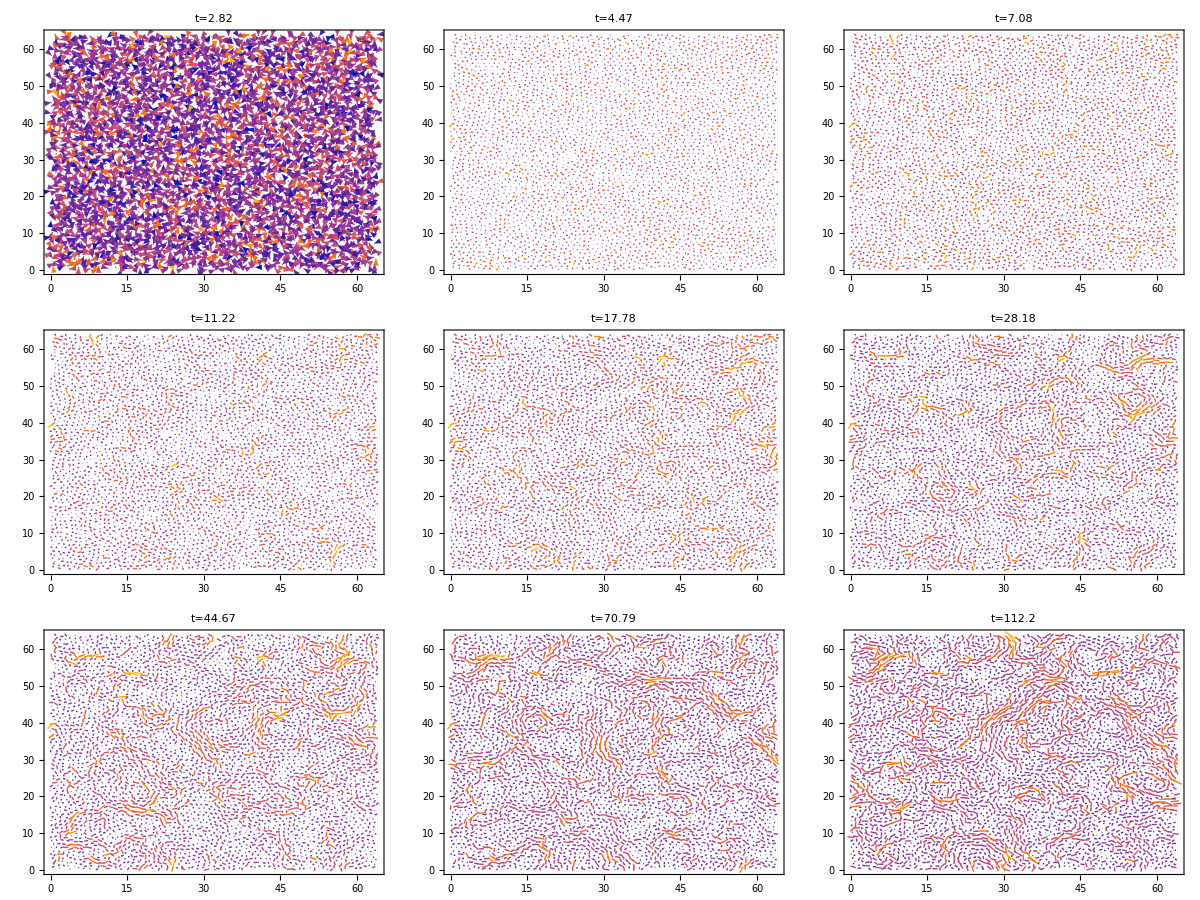

```mathematica
Grid[Partition[Table[ListVectorPlot[Table[{Partition[Normal[data[[2,3,1]]],2][[i]],displacements[[2,time,i]]},{i,4096}],VectorSizes->{0,Max[magnitudes[[2,time]]]},VectorScaling->"Linear",VectorStyle->{Thin,Arrowheads[0.01]},VectorPoints->All,VectorColorFunctionScaling->True,PlotLabel->"t="<>ToString[data[[2,4,time,1]]-data[[2,4,1,1]]],ImageSize->400],{time,40,73,4}],3]]
```

```mathematica
Grid[Partition[Table[ListStreamDensityPlot[Table[{Partition[Normal[data[[1,3,1]]],2][[i]],displacements[[1,time,i]]},{i,4096}],VectorSizes->{0,Max[magnitudes[[1,time]]]},VectorScaling->"Linear",VectorStyle->{Thin,Arrowheads[0.01]},VectorPoints->All,VectorColorFunctionScaling->True,PlotLabel->"t="<>ToString[data[[1,4,time,1]]-data[[1,4,1,1]]],ImageSize->400],{time,40,64,4}],3]]
```

-Graphics-